## Nonlinear root finding - Bisection method

The bisection method, sometimes called the binary search method, is a simple method for finding the root, or zero, of a nonlinear equation with one unknown variable. (If the equation is linear, we can solve for the root algebraically.)

If we suppose f is a continuous function defined on the interval [a,b], with f(a) and f(b) of opposite sign (e.g., they appear of opposite sides of the root).  Then there exists a point p within the interval [a,b] with f(p)=0.  We start the iteration by choosing a point halfway between a and b and checking the sign of f(p).  It will either have the same sign as f(a) or f(b).  If the sign of f(p) is the same as f(a). Then p gets set to a and the process is repeated.  If the sign of f(p) is the same as f(b), then p gets set to b and the process is repeated.

An animation showing the root of the function f(x) = cos(x) - x^3 converging to a tolerance of 0.05 follows:

```mathematica
f[x_]=Cos[x]-x^3;
xrange={0,1.5};
{a,b}={0.1,1.2};
i=1;

plot=Plot[f[x],{x,xrange[[1]],xrange[[2]]}];
lines=Graphics[{Red,Thick,Line[{{a,0},{a,f[a]}}],Line[{{b,0},{b,f[b]}}]}];
textAB=Graphics[{Red,Text[Subscript["a", 0],{a,f[a]+0.1}],Text[Subscript["b", 0],{b,0.1}]}];
animatePlot={Show[plot,lines,textAB,ImageSize->Large]};


TOL=0.05;
FA=f[a];

While [i<10000,
p=a+(b-a)/2;
FP=f[p];


pLine=Graphics[{Black,Dashed,Thick,Line[{{p,0},{p,f[p]}}]}];
textP=Graphics[Text[Subscript["p", i-1],{p,If[p>0.871875,0.1,f[p]+0.1]}]];
AppendTo[animatePlot,Show[plot,lines,textAB,pLine,textP,ImageSize->Large]];



If[FP==0 ||(b-a)/2<TOL,
Break[]
];
i=i+1;
If[Sign[FA]Sign[FP]>0,
a=p;
FA=FP,
b=p
];

lines=Graphics[{Red,Thick,Line[{{a,0},{a,f[a]}}],Line[{{b,0},{b,f[b]}}]}];
textAB=Graphics[{Red,Text[Subscript["a", i-1],{a,f[a]+0.1}],Text[Subscript["b", i-1],{b,0.1}]}];
AppendTo[animatePlot,Show[plot,lines,textAB,ImageSize->Large]];

]
If[i==10000,Print["Method failed to converge in 10000 iterations"]]
ListAnimate[animatePlot,0.5]
```

◀     |     ▶

## Psuedocode for Bisection method.

The bisection method finds a solution to f(x)=0 where f is continuously defined on the interval [a,b] and f(a) and f(b) have opposite signs:

Step 1.		Set i=1
Step 2.		Set  FA=f(a)
Step 3.		While i ≤ max iterations, do Steps 4-11
			Step 4.  Set p=a+(b-a)/2
			Step 5.  Set FP=f(p)
			
			Step 6.  If FP= 0  or  (b-a)/2 < TOL,  end program, output p as the root.
			
			Step 7.  If sign(FA)·sign(FP) > 0, then do Steps 8-9, else do Step 10
					Step 8.   a=p
					Step 9.  FA = FP
			Step 10.  Else, b=p
			Step 11.  Set i=i+1
			
Step 12.  Print "Method failed to converge after 'max iterations'."

◀     |     ▶

## Other stop procedures and convergence of the Bisection method.

Other stopping procedure can be applied at Step 6 in the previous pseudocode.  For example we can select a tolerance ϵ and generate p_1,p_2,... , p_N until one of the following conditions is met.

	|p_N-p_(N-1)| < ϵ

(|p_N-p_(N-1)|)/(|p_N|) < ϵ

|f(p_N)|<ϵ
	
The Bisection method has the advantage that as long as the root is bounded by the interval [a,b], it will always converge.  It has the disadvantage that convergence can be very slow and a good intermediate approximation to the root can be inadvertently discarded.  This method is most useful when used to get an initial very rough approximation to a root and then combine it with a method that has faster convergence to get a better approximation to the root.  We will talk about these other methods in the upcoming slides.

Let's have a look at the convergence rate of this method:

Suppose that f ∈ C[a,b] and f(a)·f(b) < 0.  The Bisection method generates a sequence {p_n-p}_(n=1)^∞ approximating a zero p of f with:

	|p_n-p|≤ (b-a)/2^n, when n≥ 1.
	
Proof:  For each n≥1, we have

	b_n-a_n=1/2^(n-1)(b-a) and p ∈ (a_n,b_n)
Since p_n=1/2(a_n+b_n) for all n≥ 1, then

	|p_n-p|<1/2(b_n-a_n)=(b-a)/2^n
	
Since,

	|p_n-p|≤ (b-a)1/2^n
	
the sequence {p_n}_(n=1)^∞ converges to p with rate of convergence O(1/2^n), i.e.

	p_n=p+O(1/2^n).

◀     |     ▶

## Nonlinear root finding - Newton-Raphson (Newton's method)

The Newton-Raphson method is most commonly used when a function of a single variable is defined mathematically (not a results of other numerical computations) and the derivative of the function can be easily evaluated.  The method approximates a function by it's tangent line at an point to get successively better estimates of the root.

For a function

f(x) = 0

The general formula is as follows:

x_(n+1)= x_n- (f(x_n))/(f'(x_n))

An example:  One iteration of the function f(x)=x^2- 25.

```mathematica
f[x_]=x^2-25; x0=6;

x1=x0-f[x0]/f'[x0]//N
```

5.08333

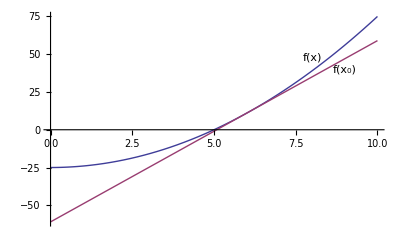

```mathematica
plot=Plot[{f[x],f'[x0](x-x0)+f[x0]},{x,0,10}];
text=Graphics[{Text["f(x)",{8,48}],Text["f(x_0)",{9,40}]}];
Show[plot,text]
```

◀     |     ▶

## Stop Condition

We continue the successive iterations until some critical tolerance criterion has been met.  The tolerance criterion can be defined as follows:

| x_(n+1)-x_n|<ϵ

An animation showing the root of the function f(x) = cos(x) - x^3 converging to a tolerance of 0.001.  An initial guess of 0.5 was used.

```mathematica
f[x_]=Cos[x]-x^3;
xRange={0,1.5};
plot=Plot[f[x],{x,xRange[[1]],xRange[[2]]},ImageSize->Large];

guess=0.5;
xNew=guess;
xOld=0;
iter=0;

animatePlot ={plot};
guessLine=Show[plot,ListLinePlot[{{guess,0},{guess,f[guess]}},PlotStyle->{Dashed,Black}],Graphics[Text[Subscript["x", iter],{guess, f[guess]+0.1}]],ImageSize->Large];
AppendTo[animatePlot,guessLine];
tangentLine=Show[guessLine,Plot[f'[guess](x-guess)+f[guess],{x,xRange[[1]],xRange[[2]]},PlotStyle->{Red}],ImageSize->Large];
AppendTo[animatePlot,tangentLine];

While[Abs[xNew-xOld] ≥ 0.001,
xOld=xNew;
xNew+=-f[xNew]/f'[xNew];

iter+=1;
guessLine=Show[plot,Plot[f'[xOld](x-xOld)+f[xOld],{x,xRange[[1]],xRange[[2]]},PlotStyle->{Red}],ListLinePlot[{{xNew,0},{xNew,f[xNew]}},PlotStyle->{Dashed,Black}],Graphics[Text[Subscript["x", iter],{xNew,f[xNew]+0.1}]],ImageSize->Large];
AppendTo[animatePlot,guessLine];
tangentLine=Show[guessLine,Plot[f'[xNew](x-xNew)+f[xNew],{x,xRange[[1]],xRange[[2]]},PlotStyle->{Red}],ImageSize->Large];
AppendTo[animatePlot,tangentLine];

]

ListAnimate[animatePlot,0.5]
```

◀     |     ▶

## Pseudocode for Newton's method.

To find a solution to f(x)=0 given an initial guess p_0:

Step 1.  Set i=1

Step 2.  While i≤ max iterations, do Steps 3-6
		Step 3.  Set p=p_0-f(p_0)/f'(p_0)
		
		Step 4.  If |p-p_0|<TOL, end program and out p as approximate root.
		
		Step 5.  Set i=i+1
		Step 6.  Set p_0=p
		
Step 7.  Print "Method failed to converge after 'max iterations'."

◀     |     ▶

## Convergence of Newton's method.

Assume that Newton's x_(k+1) iteration converges to x^* with f(x^*)≠ 0.  If we define

	x_k=x^*+ϵ_k
	
and take the Taylor series expansion about x^* we have

	f(x_k)=f(x^*)+f'(x^*)ϵ_k+1/2 f''(x^*)ϵ_k^2+…
	          = f'(x^*)ϵ_k+1/2 f''(x^*)ϵ_k^2+…
	f'(x_k)=f'(x^*)+f''(x^*)ϵ_k+…
	
But,

	ϵ_(k+1)=ϵ_k+(x_(k+1)-x_k)
	        = ϵ_k-(f(x_k))/(f'(x_k))
	        ≈ ϵ_k-(f'(x^*)ϵ_k+1/2 f''(x^*)ϵ_k^2)/(f'(x^*)+f''(x^*)ϵ_k)
	        ≈ (f''(x^*))/(2f'(x^*))ϵ_k^2
	     
The last equation implies that Newton's method converges quadratically.  That is, near a root, the number of significant digits approximately doubles with each step.  This is a very strong convergence property and makes Newton's method the root finding method of choice for any function whose derivative can be evaluated efficiently and is continuous near the root.

◀     |     ▶

## Nonlinear root finding - Secant method

In the last lecture we discussed Newton's method for root finding.  We said that although Newton's method has some very strong convergence properties, one disadvantage is the need to be able to evaluate f'(x), which can sometimes be messy.  In order to circumvent this derivative calculation we introduce a slight variation.  Recall, that by definition:

	f'(x_(n-1))= lim_(x→ x_(n-1)) (f(x)-f(x_(n-1)))/(x-x_(n-1))
	
If we let x=x_(n-2), we have,

	f'(x_(n-1))≈(f(x_(n-2))-f(x_(n-1)))/(x_(n-1)-x_(n-2))=(f(x_(n-1))-f(x_(n-2)))/(x_(n-2)-x_(n-1))
	
Substituting this expression for the derivative into Newton's formula, we have:

	x_n=x_(n-1)-(f(x_(n-1))(x_(n-1)-x_(n-2)))/(f(x_(n-1))-f(x_(n-2))).
	
This technique is called the secant method.   Here we need two initial approximations x_0 and x_1, although they need not bound the root.

◀     |     ▶

## Secant method examples

An animation showing the root of the function f(x) = cos(x) - x^3 converging to a tolerance of 0.05.  An initial guesses of 0.1 and 1.4 were used.

```mathematica
f[x_]=Cos[x]-x^3;
xrange={0,1.5};
p={0.1,1.4};
i=2;
TOL=0.05;

q={f[p[[1]]],f[p[[2]]]};

plot1=Plot[f[x],{x,xrange[[1]],xrange[[2]]}];
plot2=Plot[q[[1]]+((q[[2]]-q[[1]])/(p[[2]]-p[[1]]))(x-p[[1]]),{x,xrange[[1]],xrange[[2]]},PlotStyle->{Thick,Black}];
lines=Graphics[{Red,Thick,Line[{{p[[1]],0},{p[[1]],q[[1]]}}],Line[{{p[[2]],0},{p[[2]],q[[2]]}}]}];

textAB=Graphics[{Red,Text[Subscript["p", 0],{p[[1]],If[p[[1]]>0.871875,0.1,f[p[[1]]]+0.1]}],Text[Subscript["p", 1],{p[[2]],If[p[[2]]>0.871875,0.1,f[p[[2]]]+0.1]}]}];
animatePlot={Show[plot1,plot2,lines,textAB,ImageSize->Large]};

While[ i≤ 10000,

pTemp=p[[2]]-q[[2]](p[[2]]-p[[1]])/(q[[2]]-q[[1]]);

pLine=Graphics[{Black,Dashed,Thick,Line[{{pTemp,0},{pTemp,f[pTemp]}}]}];
textP=Graphics[Text[Subscript["p", i],{pTemp,If[pTemp>0.871875,0.1,f[pTemp]+0.1]}]];
AppendTo[animatePlot,Show[plot1,plot2,lines,textAB,pLine,textP,ImageSize->Large]];

If[Abs[pTemp-p[[2]]]<TOL,
Break[]
];


p1old=p[[1]];
p[[1]]=p[[2]];
q[[1]]=q[[2]];
p[[2]]=pTemp;
q[[2]]=f[pTemp];

plot2=Plot[q[[1]]+((q[[2]]-q[[1]])/(p[[2]]-p[[1]]))(x-p[[1]]),{x,xrange[[1]],xrange[[2]]},PlotStyle->{Thick,Black}];
lines=Graphics[{Red,Thick,Line[{{p[[1]],0},{p[[1]],q[[1]]}}],Line[{{p[[2]],0},{p[[2]],q[[2]]}}]}];
textAB=Graphics[{Red,Text[Subscript["p", i-1],{p[[1]],If[p[[1]]>0.871875,0.1,f[p[[1]]]+0.1]}],Text[Subscript["p", i],{p[[2]],If[p[[2]]>0.871875,0.1,f[p[[2]]]+0.1]}]}];
AppendTo[animatePlot,Show[plot1,plot2,lines,textAB,ImageSize->Large]];

i++;

If[i==10000,
Print["Method failed to converge in 10000 iterations"];
Break[];
];
];
ListAnimate[animatePlot,0.5]
```

This is another simulation of the same problem, this time initial guesses of 1.2 and 1.4 were used.  This demonstrates that the initial guesses for the secant method do not require one to bound the root.

```mathematica
f[x_]=Cos[x]-x^3;
xrange={0,1.5};
p={1.2,1.4};
i=2;
TOL=0.05;

q={f[p[[1]]],f[p[[2]]]};

plot1=Plot[f[x],{x,xrange[[1]],xrange[[2]]}];
plot2=Plot[q[[1]]+((q[[2]]-q[[1]])/(p[[2]]-p[[1]]))(x-p[[1]]),{x,xrange[[1]],xrange[[2]]},PlotStyle->{Thick,Black}];
lines=Graphics[{Red,Thick,Line[{{p[[1]],0},{p[[1]],q[[1]]}}],Line[{{p[[2]],0},{p[[2]],q[[2]]}}]}];

textAB=Graphics[{Red,Text[Subscript["p", 0],{p[[1]],If[p[[1]]>0.871875,0.1,f[p[[1]]]+0.1]}],Text[Subscript["p", 1],{p[[2]],If[p[[2]]>0.871875,0.1,f[p[[2]]]+0.1]}]}];
animatePlot={Show[plot1,plot2,lines,textAB,ImageSize->Large]};

While[ i≤ 10000,

pTemp=p[[2]]-q[[2]](p[[2]]-p[[1]])/(q[[2]]-q[[1]]);

pLine=Graphics[{Black,Dashed,Thick,Line[{{pTemp,0},{pTemp,f[pTemp]}}]}];
textP=Graphics[Text[Subscript["p", i],{pTemp,If[pTemp>0.871875,0.1,f[pTemp]+0.1]}]];
AppendTo[animatePlot,Show[plot1,plot2,lines,textAB,pLine,textP,ImageSize->Large]];

If[Abs[pTemp-p[[2]]]<TOL,
Break[]
];


p1old=p[[1]];
p[[1]]=p[[2]];
q[[1]]=q[[2]];
p[[2]]=pTemp;
q[[2]]=f[pTemp];

plot2=Plot[q[[1]]+((q[[2]]-q[[1]])/(p[[2]]-p[[1]]))(x-p[[1]]),{x,xrange[[1]],xrange[[2]]},PlotStyle->{Thick,Black}];
lines=Graphics[{Red,Thick,Line[{{p[[1]],0},{p[[1]],q[[1]]}}],Line[{{p[[2]],0},{p[[2]],q[[2]]}}]}];
textAB=Graphics[{Red,Text[Subscript["p", i-1],{p[[1]],If[p[[1]]>0.871875,0.1,f[p[[1]]]+0.1]}],Text[Subscript["p", i],{p[[2]],If[p[[2]]>0.871875,0.1,f[p[[2]]]+0.1]}]}];
AppendTo[animatePlot,Show[plot1,plot2,lines,textAB,ImageSize->Large]];

i++;

If[i==10000,
Print["Method failed to converge in 10000 iterations"];
Break[];
];
];
ListAnimate[animatePlot,0.5]
```

◀     |     ▶

## Pseudocode for Secant method.

To find a solution to f(x)=0 given an initial guess p_0 and p_1:

Step 1.  Set i=2
Step 2.  Set q_0=f(p_0)
Step 3.  Set q_1=f(p_1)

Step 4.  While i≤ max iterations, do Steps 5-12
		Step 5.  Set p=p_1-q_1(p_1-p_0)/(q_1-q_0)
		
		Step 6.  If |p-p_1|<TOL, end program and out p as approximate root.
		
		Step 7.  Set i=i+1
		Step 8.  Set p_0=p_1
		Step 9.  Set q_0=q_1
		Step 10.  Set p_1=p
		Step 11.  Set q_1=f(p)
		Step 12.  Set i=i+1
		
Step 13.  Print "Method failed to converge after 'max iterations'."

◀     |     ▶

## Convergence and other comments.

It can be shown that the order of convergence of the secant method is the "golden ratio"

	α=(1+√5)/2≈1.618
	
This means that the error follows the following relationship:

	lim_(k→∞) |ϵ_(k+1)|≈ constant × |ϵ_k|^α
	
The secant method has the disadvantage that the root does not necessarily remain bracketed.  For function that are not sufficiently continuous, the algorithm is not guaranteed to converge.  Local behavior might send it off toward infinity.  There is a slight modification to the secant method called the false position method that will keep the root bracketed and therefore guarantee convergence, but at a slower rate.  A better method to grantee convergence would be to combine the secant method with the bisection method, therefore we will not discuss the false position method.

◀     |     ▶

## Hybrid methods.

Hybrid methods simply combine two or more root finding methods to create a robust algorithm.  Here I have combined the bisection method with the secant method.  The bisection method is used to get near the root, then the secant method is used to polish it off.  This is for the same function used in previous examples f(x) = cos(x) - x^3.

```mathematica
f[x_]=Cos[x]-x^3;
xrange={0,1.5};
{a,b}={0.1,1.4};
i=1;

plot=Plot[f[x],{x,xrange[[1]],xrange[[2]]}];
lines=Graphics[{Red,Thick,Line[{{a,0},{a,f[a]}}],Line[{{b,0},{b,f[b]}}]}];
textAB=Graphics[{Red,Text[Subscript["a", 0],{a,f[a]+0.1}],Text[Subscript["b", 0],{b,0.1}]}];
animatePlot={Show[plot,lines,textAB,ImageSize->Large]};


TOL=0.05;
FA=f[a];

While [i<10000,
p=a+(b-a)/2;
FP=f[p];


pLine=Graphics[{Black,Dashed,Thick,Line[{{p,0},{p,f[p]}}]}];
textP=Graphics[Text[Subscript["p", i-1],{p,If[p>0.871875,0.1,f[p]+0.1]}]];
AppendTo[animatePlot,Show[plot,lines,textAB,pLine,textP,ImageSize->Large]];

i=i+1;
If[Sign[FA]Sign[FP]>0,
a=p;
FA=FP,
b=p
];


lines=Graphics[{Red,Thick,Line[{{a,0},{a,f[a]}}],Line[{{b,0},{b,f[b]}}]}];
textAB=Graphics[{Red,Text[Subscript["a", i-1],{a,f[a]+0.1}],Text[Subscript["b", i-1],{b,0.1}]}];
AppendTo[animatePlot,Show[plot,lines,textAB,ImageSize->Large]];

If[FP==0 ||(b-a)/2<0.2,
Break[]
];

]
If[i==10000,Print["Method failed to converge in 10000 iterations"]]

p={a,b};
i=2;
TOL=0.05;

q={f[p[[1]]],f[p[[2]]]};

plot1=Plot[f[x],{x,xrange[[1]],xrange[[2]]}];
plot2=Plot[q[[1]]+((q[[2]]-q[[1]])/(p[[2]]-p[[1]]))(x-p[[1]]),{x,xrange[[1]],xrange[[2]]},PlotStyle->{Thick,Black}];
lines=Graphics[{Red,Thick,Line[{{p[[1]],0},{p[[1]],q[[1]]}}],Line[{{p[[2]],0},{p[[2]],q[[2]]}}]}];

textAB=Graphics[{Red,Text[Subscript["p", 0],{p[[1]],If[p[[1]]>0.871875,0.1,f[p[[1]]]+0.1]}],Text[Subscript["p", 1],{p[[2]],If[p[[2]]>0.871875,0.1,f[p[[2]]]+0.1]}]}];
AppendTo[animatePlot,Show[plot1,plot2,lines,textAB,ImageSize->Large]];

While[ i≤ 10000,

pTemp=p[[2]]-q[[2]](p[[2]]-p[[1]])/(q[[2]]-q[[1]]);

pLine=Graphics[{Black,Dashed,Thick,Line[{{pTemp,0},{pTemp,f[pTemp]}}]}];
textP=Graphics[Text[Subscript["p", i],{pTemp,If[pTemp>0.871875,0.1,f[pTemp]+0.1]}]];
AppendTo[animatePlot,Show[plot1,plot2,lines,textAB,pLine,textP,ImageSize->Large]];

If[Abs[pTemp-p[[2]]]<TOL,
Break[]
];


p1old=p[[1]];
p[[1]]=p[[2]];
q[[1]]=q[[2]];
p[[2]]=pTemp;
q[[2]]=f[pTemp];

plot2=Plot[q[[1]]+((q[[2]]-q[[1]])/(p[[2]]-p[[1]]))(x-p[[1]]),{x,xrange[[1]],xrange[[2]]},PlotStyle->{Thick,Black}];
lines=Graphics[{Red,Thick,Line[{{p[[1]],0},{p[[1]],q[[1]]}}],Line[{{p[[2]],0},{p[[2]],q[[2]]}}]}];
textAB=Graphics[{Red,Text[Subscript["p", i-1],{p[[1]],If[p[[1]]>0.871875,0.1,f[p[[1]]]+0.1]}],Text[Subscript["p", i],{p[[2]],If[p[[2]]>0.871875,0.1,f[p[[2]]]+0.1]}]}];
AppendTo[animatePlot,Show[plot1,plot2,lines,textAB,ImageSize->Large]];

i++;

If[i==10000,
Print["Method failed to converge in 10000 iterations"];
Break[];
];
];
ListAnimate[animatePlot,0.5]
```

◀     |     ▶